## Method_a

```mathematica
F[qsq_]:= ef1+ef2 qsq + ef3 qsq^2 ;
```

```mathematica
G[qsq_]:= eg1+eg2 qsq + eg3 qsq^2 ;
```

```mathematica
FCovMat={{0.05,0.0,0.0},{0.00,0.04,0.00},{0,0,0.03}};
```

```mathematica
GCovMat={{0.044,0.0,0},{0.0,0.033,0},{0,0,0.022}};
```

```mathematica
(*MatrixForm[FCovMat]*)
```

```mathematica
varF[qsq_]:={{ef1,ef2 qsq,ef3 qsq^2}}.FCovMat.{{ef1},{ef2 qsq},{ef3 qsq^2}}
```

```mathematica
varG[qsq_]:={{eg1,eg2 qsq,eg3 qsq^2}}.GCovMat.{{eg1},{eg2 qsq},{eg3 qsq^2}}
```

```mathematica
erFfun[qsq_]:=√Expand[varF[qsq][[1,1]]]
```

```mathematica
erGfun[qsq_]:=√Expand[varG[qsq][[1,1]]]
```

```mathematica
obs[qsq_]:=F[qsq]/G[qsq] ;
```

```mathematica
Clear[F,G]
```

```mathematica
errobs[qsq_]:=√((D[obs[qsq],F[qsq]]erFfun[qsq])^2+(D[obs[qsq],G[qsq]]erGfun[qsq])^2);
```

```mathematica
sub={F[qsq]-> ef1+ef2 qsq+ef3 qsq^2  ,G[qsq]-> eg1+eg2 qsq+eg3 qsq^2  };
```

```mathematica
obs[qsq]//.sub//.{ef1->0.5,ef2->0.4,ef3->0.3,eg1->0.44,eg2->0.33,eg3->0.22,qsq->4.5}
```

1.3127

```mathematica
errobs[qsq]//.sub//.{ef1->0.5,ef2->0.4,ef3->0.3,eg1->0.44,eg2->0.33,eg3->0.22,qsq->4.5}
```

0.229384

## Method_b

```mathematica
F[qsq_]:= a1+b1 qsq + c1 qsq^2 ;
```

```mathematica
G[qsq_]:= a2+b2 qsq + c2 qsq^2 ;
```

```mathematica
a1=0.5;b1=0.4;c1=0.3;a2=0.44;b2=0.33;c2=0.22;
ma1=0.5;mb1=0.4;mc1=0.3;ea1=0.05;eb1=0.04;ec1=0.03;
ma2=0.44;mb2=0.33;mc2=0.22;ea2=0.044;eb2=0.033;ec2=0.022;
```

```mathematica
mnd[μ_,σ_]:=Random[NormalDistribution[μ,σ]]
```

```mathematica
simF[qsq_]:=mnd[ma1,ea1]+mnd[mb1,eb1] qsq+mnd[mc1,ec1] qsq^2;
```

```mathematica
simG[qsq_]:=mnd[ma2,ea2]+mnd[mb2,eb2] qsq+mnd[mc2,ec2] qsq^2;
```

```mathematica
obs[qsq_]:=F[qsq]/G[qsq] ;
```

```mathematica
simobs[qsq_]:=simF[qsq]/simG[qsq] ;
```

```mathematica
qsq=4.5;
```

```mathematica
iter=100000;
```

```mathematica
simlst={};
```

```mathematica
Do[AppendTo[simlst,simobs[qsq]],iter];
```

```mathematica
Length[simlst]
```

100000

```mathematica
{Mean[simlst],StandardDeviation[simlst]}
```

{1.31966,0.140718}

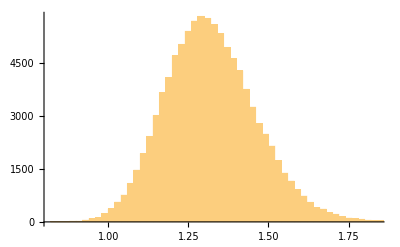

```mathematica
Histogram[simlst,50]
```